g2 graph 21b
level 3

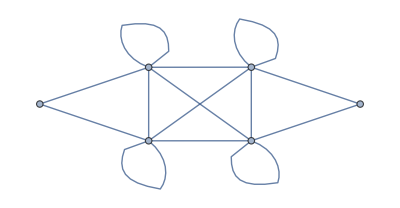

```mathematica
SetDirectory["~/Documents/UNH/Research/code/github/graph_21b"];
graph = { 
{0,1,0,0,0,1},
{1,1,1,0,1,1},
{0,1,1,1,1,1},
{0,0,1,0,1,0},
{0,1,1,1,1,1},
{1,1,1,0,1,1}
 };
AdjacencyGraph[ graph] (* picture of the graph *)
Clear[aa,bb,cc,dd,ee,ff,gg,hh,ii,jj,kk,ll,mm,nn,oo,pp,qq,rr,ss,tt,uu,vv,ww,xx];
SetNonCommutative[aa,bb,cc,dd,ee,ff,gg,hh,ii,jj,kk,ll,mm,nn,oo,pp,qq,rr,ss,tt,uu,vv,ww,xx];
CGamma = { 
{0,aa,0,0,0,bb},
{cc,dd,ee,0,ff,gg},
{0,hh,ii,jj,kk,ll},
{0,0,mm,0,nn,0},
{0,oo,pp,qq,rr,ss},
{tt,uu,vv,0,ww,xx}
};
level=4;
q=Exp[Pi*I/(3*(4+level))]; (* see physics paper *)
```

Data import

```mathematica
linearEqns = Import["./data/linearEqns.m"];
linearSol = Solve[linearEqns][[1]];
bigonEqns = Import["./data/bigonEqns.m"];
trigonEqns = Import["./data/trigonEqns.m"];
traceEqns = Import["./data/traceEqns.m"];
reducedLoEqns = Import["./data/reducedLo.m"];
squareEqns = Import["./data/squareEqns.m"];
pentEqns = Import["./data/pentEqns.m"];
reducedHiEqns = Import["./data/reducedHi.m"];
```

```mathematica
loVariables=Union@Cases[reducedLoEqns,_Symbol,Infinity];
loVariables = DeleteCases[loVariables, True];
loVariables = DeleteCases[loVariables, Pi]
loVariables//Length
```

{alpha10,alpha11,alpha30,alpha31,alpha32,alpha33,alpha50,alpha55,alpha61,alpha62,alpha63,alpha64,alpha69,alpha73,alpha74,alpha78,alpha8,alpha85,alpha86,alpha87,alpha88,alpha9}

22

```mathematica
loVariables=Union@Cases[reducedHiEqns,_Symbol,Infinity];
loVariables = DeleteCases[loVariables, True];
loVariables = DeleteCases[loVariables, Pi]
loVariables//Length
```

{alpha10,alpha11,alpha30,alpha31,alpha32,alpha33,alpha50,alpha55,alpha61,alpha62,alpha63,alpha64,alpha69,alpha73,alpha74,alpha78,alpha8,alpha85,alpha86,alpha87,alpha88,alpha9}

22

Scratch work.

```mathematica
reducedLoEqns//TableForm
```

True
1/6 (-3+√3+√6) (alpha69^2+(1+√(3/2)) alpha8^2)==1
1/6 (-3+√3+√6) (alpha69^2+(1+√(3/2)) alpha85^2)==1
(-3+√3+√6) alpha69^2+((3-√3+√6) alpha8^2)/(√2)==6
1/6 (-3+√3+√6) (alpha10^2+alpha11^2+alpha8^2+alpha9^2+(alpha10+alpha11+√(-2+√6) alpha8+alpha9)^2)==1
1/6 (-3+√3+√6) (alpha30^2+alpha50^2+alpha73^2+alpha9^2)==1
1/6 (-3+√3+√6) (alpha10^2+alpha50^2+alpha61^2+alpha74^2)==1
1/6 (-3+√3+√6) (alpha11^2+(-2+√6) alpha69^2+alpha73^2+alpha74^2+alpha86^2)==1
1/6 (-3+√3+√6) (alpha30^2+alpha31^2+alpha32^2+alpha33^2+(alpha30+√(-2+√6) alpha31+alpha32+alpha33)^2)==1
((3-√3+√6) (alpha31^2+alpha55^2))/(√2)==6
1/6 (-3+√3+√6) (alpha32^2+alpha50^2+alpha55^2+alpha62^2+alpha78^2)==1
1/6 (-3+√3+√6) (alpha33^2+alpha73^2+alpha78^2+alpha87^2)==1
((3-√3+√6) (alpha31^2+alpha55^2))/(6 √2)==1
((3-√3+√6) (alpha55^2+alpha63^2))/(6 √2)==1
((3-√3+√6) (alpha55^2+alpha63^2))/(√2)==6
1/6 (-3+√3+√6) (alpha61^2+alpha62^2+alpha63^2+alpha64^2+(alpha61+alpha62+√(-2+√6) alpha63+alpha64)^2)==1
1/6 (-3+√3+√6) (alpha64^2+alpha74^2+alpha78^2+alpha88^2)==1
(-3+√3+√6) alpha69^2+((3-√3+√6) alpha85^2)/(√2)==6
1/6 (-3+√3+√6) (alpha85^2+alpha86^2+alpha87^2+alpha88^2+(√(-2+√6) alpha85+alpha86+alpha87+alpha88)^2)==1
(√2+√3) ((2+√6) alpha69^2+(5+2 √6) alpha8^2)==27+6 √2+5 √3+11 √6
(√2+√3) ((2+√6) alpha69^2+(5+2 √6) alpha85^2)==27+6 √2+5 √3+11 √6
alpha10^2+alpha11^2+alpha8^2+alpha9^2+(alpha10+alpha11+√(-2+√6) alpha8+alpha9)^2==(3+√3+√6)/(√2)
√(-2+√6) alpha69^2+√(1+√(3/2)) alpha8^2==√6 (2+√3)^(1/4)
alpha30^2+alpha50^2+alpha73^2+alpha9^2==(3+√3+√6)/(√2)
alpha10^2+alpha50^2+alpha61^2+alpha74^2==(3+√3+√6)/(√2)
alpha11^2+(-2+√6) alpha69^2+alpha73^2+alpha74^2+alpha86^2==(3+√3+√6)/(√2)
alpha30^2+alpha31^2+alpha32^2+alpha33^2+(alpha30+√(-2+√6) alpha31+alpha32+alpha33)^2==(3+√3+√6)/(√2)
√(2+√6) (alpha31^2+alpha55^2)==2 √3 (2+√3)^(1/4)
alpha32^2+alpha50^2+alpha55^2+alpha62^2+alpha78^2==(3+√3+√6)/(√2)
alpha33^2+alpha73^2+alpha78^2+alpha87^2==(3+√3+√6)/(√2)
2 (√2+√3) (alpha31^2+alpha55^2)==2 (3+√3+√6)
2 (√2+√3) (alpha55^2+alpha63^2)==2 (3+√3+√6)
alpha61^2+alpha62^2+alpha63^2+alpha64^2+(alpha61+alpha62+√(-2+√6) alpha63+alpha64)^2==(3+√3+√6)/(√2)
√(2+√6) (alpha55^2+alpha63^2)==2 √3 (2+√3)^(1/4)
alpha64^2+alpha74^2+alpha78^2+alpha88^2==(3+√3+√6)/(√2)
alpha85^2+alpha86^2+alpha87^2+alpha88^2+(√(-2+√6) alpha85+alpha86+alpha87+alpha88)^2==(3+√3+√6)/(√2)
√(-2+√6) alpha69^2+√(1+√(3/2)) alpha85^2==√6 (2+√3)^(1/4)
alpha11 alpha69^2+√(1+√(3/2)) (1+√3) alpha8==(1+√(3/2)) alpha8^2 (alpha10+alpha11+√(-2+√6) alpha8+alpha9)
(1+√3) alpha69+√(1+√(3/2)) alpha69 (alpha11 alpha8+alpha85 alpha86)==0
alpha69^2 alpha86==1/2 √(1+√(3/2)) alpha85 (-2 (1+√3)+2 alpha85^2+√(2 (2+√6)) alpha85 (alpha86+alpha87+alpha88))
alpha10^3+alpha11^3+√(1+√(3/2)) alpha8^3+alpha9^3==alpha10+alpha11+√(-2+√6) alpha8+alpha9+√3 (alpha10+alpha11+√(-2+√6) alpha8+alpha9)+(alpha10+alpha11+√(-2+√6) alpha8+alpha9)^3
√(1+√(3/2)) ((-2+√6) alpha11 alpha69^2-alpha8^2 (alpha10+alpha11+√(-2+√6) alpha8+alpha9))==-((1+√3) alpha8)
alpha10 alpha50^2+alpha11 alpha73^2+(1+√3+alpha30^2) alpha9==alpha9^2 (alpha10+alpha11+√(-2+√6) alpha8+alpha9)
alpha10 (1+√3+alpha61^2)+alpha11 alpha74^2+alpha50^2 alpha9==alpha10^2 (alpha10+alpha11+√(-2+√6) alpha8+alpha9)
alpha10 alpha74^2+√(-2+√6) alpha69^2 alpha8+alpha11 (1+√3+alpha86^2)+alpha73^2 alpha9==alpha11^2 (alpha10+alpha11+√(-2+√6) alpha8+alpha9)
alpha10 alpha50^2+alpha11 alpha73^2+(1+√3+alpha30^2) alpha9==alpha9^2 (alpha10+alpha11+√(-2+√6) alpha8+alpha9)
alpha32 alpha50^2+alpha33 alpha73^2+alpha30 (1+√3+alpha9^2)==alpha30^2 (alpha30+√(-2+√6) alpha31+alpha32+alpha33)
alpha73 alpha74 alpha78+alpha50 (1+√3+alpha30 alpha32+alpha61 alpha62+alpha10 alpha9)==0
alpha50 alpha74 alpha78+alpha73 (1+√3+alpha30 alpha33+alpha86 alpha87+alpha11 alpha9)==0
(1+√3+alpha10^2) alpha61+alpha50^2 alpha62+alpha64 alpha74^2==alpha61^2 (alpha61+alpha62+√(-2+√6) alpha63+alpha64)
alpha50 alpha73 alpha78+alpha74 (1+√3+alpha10 alpha11+alpha61 alpha64+alpha86 alpha88)==0
alpha69 ((1+√3) √(-2+√6)+alpha11 alpha8+alpha85 alpha86)==0
√(-2+√6) alpha69^2 alpha85+(1+√3+alpha11^2) alpha86+alpha73^2 alpha87+alpha74^2 alpha88==alpha86^2 (√(-2+√6) alpha85+alpha86+alpha87+alpha88)
alpha30^3+√(1+√(3/2)) alpha31^3+alpha32^3+alpha33^3==alpha30+√(-2+√6) alpha31+alpha32+alpha33+√3 (alpha30+√(-2+√6) alpha31+alpha32+alpha33)+(alpha30+√(-2+√6) alpha31+alpha32+alpha33)^3
√(1+√(3/2)) (-alpha31^2 (alpha30+√(-2+√6) alpha31+alpha32+alpha33)+alpha32 alpha55^2)==-((1+√3) alpha31)
alpha30 alpha50^2+√(1+√(3/2)) alpha31 alpha55^2+alpha32 (1+√3+alpha62^2)+alpha33 alpha78^2==alpha32^2 (alpha30+√(-2+√6) alpha31+alpha32+alpha33)
alpha30 alpha73^2+alpha32 alpha78^2+alpha33 (1+√3+alpha87^2)==alpha33^2 (alpha30+√(-2+√6) alpha31+alpha32+alpha33)
√(2+√6) (3+√2+√3+√6) alpha31+(5+2 √6) alpha32 alpha55^2==(5+2 √6) alpha31^2 (alpha30+√(-2+√6) alpha31+alpha32+alpha33)
alpha55 (2 (1+√3)+√(2 (2+√6)) (alpha31 alpha32+alpha62 alpha63))==0
√(1+√(3/2)) alpha55 (alpha31 alpha32+alpha62 alpha63)==-((1+√3) alpha55)
alpha50^2 alpha61+(1+√3+alpha32^2) alpha62+√(1+√(3/2)) alpha55^2 alpha63+alpha64 alpha78^2==alpha62^2 (alpha61+alpha62+√(-2+√6) alpha63+alpha64)
alpha50 alpha73 alpha74+alpha78 (1+√3+alpha32 alpha33+alpha62 alpha64+alpha87 alpha88)==0
alpha73^2 alpha86+(1+√3+alpha33^2) alpha87+alpha78^2 alpha88==alpha87^2 (√(-2+√6) alpha85+alpha86+alpha87+alpha88)
(-1+√(3/2)) ((5+2 √6) alpha55^2 alpha62+√(22+9 √6) alpha63 (1+√3-alpha63^2-√(1+√(3/2)) alpha63 (alpha61+alpha62+alpha64)))==0
alpha61^3+alpha62^3+√(1+√(3/2)) alpha63^3+alpha64^3==alpha61+alpha62+√(-2+√6) alpha63+alpha64+√3 (alpha61+alpha62+√(-2+√6) alpha63+alpha64)+(alpha61+alpha62+√(-2+√6) alpha63+alpha64)^3
√(1+√(3/2)) (alpha55^2 alpha62-alpha63^2 (alpha61+alpha62+√(-2+√6) alpha63+alpha64))==-((1+√3) alpha63)
alpha61 alpha74^2+alpha62 alpha78^2+alpha64 (1+√3-alpha64 (alpha61+alpha62+√(-2+√6) alpha63+alpha64)+alpha88^2)==0
alpha74^2 alpha86+alpha78^2 alpha87+alpha88 (1+√3+alpha64^2-alpha88 (√(-2+√6) alpha85+alpha86+alpha87+alpha88))==0
(5+2 √6) alpha85^2 (√(-2+√6) alpha85+alpha86+alpha87+alpha88)==(1+√3) √(22+9 √6) alpha85+(2+√6) alpha69^2 alpha86
√(1+√(3/2)) alpha85^3+alpha86^3+alpha87^3+alpha88^3==√(-2+√6) alpha85+alpha86+alpha87+alpha88+√3 (√(-2+√6) alpha85+alpha86+alpha87+alpha88)+(√(-2+√6) alpha85+alpha86+alpha87+alpha88)^3
alpha85^2 (2 alpha85+√(2 (2+√6)) (alpha86+alpha87+alpha88))==2 (alpha85+√3 alpha85+√(-2+√6) alpha69^2 alpha86)

Begin 5/22 work.

```mathematica
bigonEqns//Length
trigonEqns//Length
traceEqns//Length
squareEqns//Length
pentEqns//Length
```

24

88

24

384

1744

```mathematica
bigonEqns/.linearSol//FullSimplify//DeleteDuplicates//TableForm
```

(√2+√3) ((2+√6) alpha69^2+(5+2 √6) alpha8^2)==27+6 √2+5 √3+11 √6
(√2+√3) ((2+√6) alpha69^2+(5+2 √6) alpha85^2)==27+6 √2+5 √3+11 √6
alpha10^2+alpha11^2+alpha8^2+alpha9^2+(alpha10+alpha11+√(-2+√6) alpha8+alpha9)^2==(3+√3+√6)/(√2)
√(-2+√6) alpha69^2+√(1+√(3/2)) alpha8^2==√6 (2+√3)^(1/4)
alpha30^2+alpha50^2+alpha73^2+alpha9^2==(3+√3+√6)/(√2)
alpha10^2+alpha50^2+alpha61^2+alpha74^2==(3+√3+√6)/(√2)
alpha11^2+(-2+√6) alpha69^2+alpha73^2+alpha74^2+alpha86^2==(3+√3+√6)/(√2)
alpha30^2+alpha31^2+alpha32^2+alpha33^2+(alpha30+√(-2+√6) alpha31+alpha32+alpha33)^2==(3+√3+√6)/(√2)
√(2+√6) (alpha31^2+alpha55^2)==2 √3 (2+√3)^(1/4)
alpha32^2+alpha50^2+alpha55^2+alpha62^2+alpha78^2==(3+√3+√6)/(√2)
alpha33^2+alpha73^2+alpha78^2+alpha87^2==(3+√3+√6)/(√2)
2 (√2+√3) (alpha31^2+alpha55^2)==2 (3+√3+√6)
2 (√2+√3) (alpha55^2+alpha63^2)==2 (3+√3+√6)
alpha61^2+alpha62^2+alpha63^2+alpha64^2+(alpha61+alpha62+√(-2+√6) alpha63+alpha64)^2==(3+√3+√6)/(√2)
√(2+√6) (alpha55^2+alpha63^2)==2 √3 (2+√3)^(1/4)
alpha64^2+alpha74^2+alpha78^2+alpha88^2==(3+√3+√6)/(√2)
alpha85^2+alpha86^2+alpha87^2+alpha88^2+(√(-2+√6) alpha85+alpha86+alpha87+alpha88)^2==(3+√3+√6)/(√2)
√(-2+√6) alpha69^2+√(1+√(3/2)) alpha85^2==√6 (2+√3)^(1/4)

```mathematica
(3+√3+√6)/(√2)//Sqrt//N
```

2.25347

```mathematica
bigonEqns/.linearSol/.alpha8->alpha85//FullSimplify//DeleteDuplicates//TableForm
```

(√2+√3) ((2+√6) alpha69^2+(5+2 √6) alpha85^2)==27+6 √2+5 √3+11 √6
alpha10^2+alpha11^2+alpha85^2+alpha9^2+(alpha10+alpha11+√(-2+√6) alpha85+alpha9)^2==(3+√3+√6)/(√2)
√(-2+√6) alpha69^2+√(1+√(3/2)) alpha85^2==√6 (2+√3)^(1/4)
alpha30^2+alpha50^2+alpha73^2+alpha9^2==(3+√3+√6)/(√2)
alpha10^2+alpha50^2+alpha61^2+alpha74^2==(3+√3+√6)/(√2)
alpha11^2+(-2+√6) alpha69^2+alpha73^2+alpha74^2+alpha86^2==(3+√3+√6)/(√2)
alpha30^2+alpha31^2+alpha32^2+alpha33^2+(alpha30+√(-2+√6) alpha31+alpha32+alpha33)^2==(3+√3+√6)/(√2)
√(2+√6) (alpha31^2+alpha55^2)==2 √3 (2+√3)^(1/4)
alpha32^2+alpha50^2+alpha55^2+alpha62^2+alpha78^2==(3+√3+√6)/(√2)
alpha33^2+alpha73^2+alpha78^2+alpha87^2==(3+√3+√6)/(√2)
2 (√2+√3) (alpha31^2+alpha55^2)==2 (3+√3+√6)
2 (√2+√3) (alpha55^2+alpha63^2)==2 (3+√3+√6)
alpha61^2+alpha62^2+alpha63^2+alpha64^2+(alpha61+alpha62+√(-2+√6) alpha63+alpha64)^2==(3+√3+√6)/(√2)
√(2+√6) (alpha55^2+alpha63^2)==2 √3 (2+√3)^(1/4)
alpha64^2+alpha74^2+alpha78^2+alpha88^2==(3+√3+√6)/(√2)
alpha85^2+alpha86^2+alpha87^2+alpha88^2+(√(-2+√6) alpha85+alpha86+alpha87+alpha88)^2==(3+√3+√6)/(√2)

```mathematica
bigonEqns/.linearSol/.alpha8->alpha85/.alpha31->alpha63//FullSimplify//DeleteDuplicates//TableForm
```

(√2+√3) ((2+√6) alpha69^2+(5+2 √6) alpha85^2)==27+6 √2+5 √3+11 √6
alpha10^2+alpha11^2+alpha85^2+alpha9^2+(alpha10+alpha11+√(-2+√6) alpha85+alpha9)^2==(3+√3+√6)/(√2)
√(-2+√6) alpha69^2+√(1+√(3/2)) alpha85^2==√6 (2+√3)^(1/4)
alpha30^2+alpha50^2+alpha73^2+alpha9^2==(3+√3+√6)/(√2)
alpha10^2+alpha50^2+alpha61^2+alpha74^2==(3+√3+√6)/(√2)
alpha11^2+(-2+√6) alpha69^2+alpha73^2+alpha74^2+alpha86^2==(3+√3+√6)/(√2)
alpha30^2+alpha32^2+alpha33^2+alpha63^2+(alpha30+alpha32+alpha33+√(-2+√6) alpha63)^2==(3+√3+√6)/(√2)
√(2+√6) (alpha55^2+alpha63^2)==2 √3 (2+√3)^(1/4)
alpha32^2+alpha50^2+alpha55^2+alpha62^2+alpha78^2==(3+√3+√6)/(√2)
alpha33^2+alpha73^2+alpha78^2+alpha87^2==(3+√3+√6)/(√2)
2 (√2+√3) (alpha55^2+alpha63^2)==2 (3+√3+√6)
alpha61^2+alpha62^2+alpha63^2+alpha64^2+(alpha61+alpha62+√(-2+√6) alpha63+alpha64)^2==(3+√3+√6)/(√2)
alpha64^2+alpha74^2+alpha78^2+alpha88^2==(3+√3+√6)/(√2)
alpha85^2+alpha86^2+alpha87^2+alpha88^2+(√(-2+√6) alpha85+alpha86+alpha87+alpha88)^2==(3+√3+√6)/(√2)

```mathematica
Parallelize[
Map[RootReduce,trigonEqns/.linearSol/.alpha8->alpha85/.alpha31->alpha63]
]//DeleteDuplicates//TableForm
```

alpha11 alpha69^2+1/2 (2+√6) alpha85^2 (-alpha10-alpha11-alpha9+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)+alpha85 Root2.58Root[-9-12 #1^2+2 #1^4&,2]2.583454008527105+alpha85 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142==0
alpha69 (1+√3+alpha11 alpha85 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142+alpha85 alpha86 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142)==0
alpha69^2 alpha86+alpha85 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142 (1+√3+alpha85 (-alpha86-alpha87-alpha88+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858) Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142)==0
-alpha10+alpha10^3-alpha11+alpha11^3-alpha9+alpha9^3+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858+√3 (-alpha10-alpha11-alpha9+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)+(-alpha10-alpha11-alpha9+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)^3+alpha85^3 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142==0
((-2+√6) alpha11 alpha69^2+alpha85^2 (-alpha10-alpha11-alpha9+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)) Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142==(-1-√3) alpha85
alpha10 alpha50^2+alpha11 alpha73^2+alpha9 (1+√3+alpha30^2+alpha9 (-alpha10-alpha11-alpha9+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858))==0
alpha10+√3 alpha10+alpha10 alpha61^2+alpha11 alpha74^2+alpha50^2 alpha9+alpha10^2 (-alpha10-alpha11-alpha9+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)==0
alpha11+√3 alpha11+alpha10 alpha74^2+alpha11 alpha86^2+alpha73^2 alpha9+alpha11^2 (-alpha10-alpha11-alpha9+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)+alpha69^2 alpha85 Root0.670Root[-2+4 #1^2+#1^4&,2]0.6704399621018858==0
alpha10 alpha50^2+alpha11 alpha73^2+alpha9+√3 alpha9+alpha30^2 alpha9+alpha9^2 (-alpha10-alpha11-alpha9+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)==0
alpha30+√3 alpha30+alpha32 alpha50^2+alpha33 alpha73^2+alpha30 alpha9^2+alpha30^2 (-alpha30-alpha32-alpha33+alpha63 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)==0
alpha73 alpha74 alpha78+alpha50 (1+√3+alpha30 alpha32+alpha61 alpha62+alpha10 alpha9)==0
alpha50 alpha74 alpha78+alpha73 (1+√3+alpha30 alpha33+alpha86 alpha87+alpha11 alpha9)==0
alpha61+√3 alpha61+alpha10^2 alpha61+alpha50^2 alpha62+alpha64 alpha74^2+alpha61^2 (-alpha61-alpha62-alpha64+alpha63 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)==0
alpha50 alpha73 alpha78+alpha74 (1+√3+alpha10 alpha11+alpha61 alpha64+alpha86 alpha88)==0
alpha69 (alpha11 alpha85+alpha85 alpha86)==alpha69 Root-1.83Root[64-256 #1^2-48 #1^4+32 #1^6+#1^8&,1]-1.8316760398869047
alpha86+√3 alpha86+alpha11^2 alpha86+alpha73^2 alpha87+alpha74^2 alpha88+alpha86^2 (-alpha86-alpha87-alpha88+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)+alpha69^2 alpha85 Root0.670Root[-2+4 #1^2+#1^4&,2]0.6704399621018858==0
-alpha30+alpha30^3-alpha32+alpha32^3-alpha33+alpha33^3+alpha63 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858+√3 (-alpha30-alpha32-alpha33+alpha63 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)+(-alpha30-alpha32-alpha33+alpha63 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)^3+alpha63^3 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142==0
(alpha32 alpha55^2+alpha63^2 (-alpha30-alpha32-alpha33+alpha63 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)) Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142==(-1-√3) alpha63
alpha32+√3 alpha32+alpha30 alpha50^2+alpha32 alpha62^2+alpha33 alpha78^2+alpha32^2 (-alpha30-alpha32-alpha33+alpha63 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)+alpha55^2 alpha63 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142==0
alpha33+√3 alpha33+alpha30 alpha73^2+alpha32 alpha78^2+alpha33 alpha87^2+alpha33^2 (-alpha30-alpha32-alpha33+alpha63 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)==0
1/2 (2+√6) alpha32 alpha55^2+1/2 (2+√6) alpha63^2 (-alpha30-alpha32-alpha33+alpha63 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)+alpha63 Root2.58Root[-9-12 #1^2+2 #1^4&,2]2.583454008527105+alpha63 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142==0
alpha55 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142 (1+√3+alpha32 alpha63 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142+alpha62 alpha63 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142)==0
alpha55 (alpha32 alpha63+alpha62 alpha63) Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142==(-1-√3) alpha55
alpha50^2 alpha61+alpha62+√3 alpha62+alpha32^2 alpha62+alpha64 alpha78^2+alpha62^2 (-alpha61-alpha62-alpha64+alpha63 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)+alpha55^2 alpha63 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142==0
alpha50 alpha73 alpha74+alpha78 (1+√3+alpha32 alpha33+alpha62 alpha64+alpha87 alpha88)==0
alpha73^2 alpha86+alpha87+√3 alpha87+alpha33^2 alpha87+alpha78^2 alpha88+alpha87^2 (-alpha86-alpha87-alpha88+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)==0
1/2 (2+√6) alpha55^2 alpha62+alpha63 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142 (1+√3+alpha63 (-alpha61-alpha62-alpha64+alpha63 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858) Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142)==0
-alpha61+alpha61^3-alpha62+alpha62^3-alpha64+alpha64^3+alpha63 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858+√3 (-alpha61-alpha62-alpha64+alpha63 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)+(-alpha61-alpha62-alpha64+alpha63 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)^3+alpha63^3 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142==0
(alpha55^2 alpha62+alpha63^2 (-alpha61-alpha62-alpha64+alpha63 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)) Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142==(-1-√3) alpha63
alpha61 alpha74^2+alpha62 alpha78^2+alpha64 (1+√3+alpha88^2+alpha64 (-alpha61-alpha62-alpha64+alpha63 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858))==0
alpha74^2 alpha86+alpha78^2 alpha87+alpha88 (1+√3+alpha64^2+alpha88 (-alpha86-alpha87-alpha88+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858))==0
alpha69^2 alpha86+1/2 (2+√6) alpha85^2 (-alpha86-alpha87-alpha88+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)+alpha85 Root2.58Root[-9-12 #1^2+2 #1^4&,2]2.583454008527105+alpha85 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142==0
-alpha86+alpha86^3-alpha87+alpha87^3-alpha88+alpha88^3+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858+√3 (-alpha86-alpha87-alpha88+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)+(-alpha86-alpha87-alpha88+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)^3+alpha85^3 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142==0
((-2+√6) alpha69^2 alpha86+alpha85^2 (-alpha86-alpha87-alpha88+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)) Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142==(-1-√3) alpha85

```mathematica
Parallelize[
Map[RootReduce,traceEqns/.linearSol/.alpha8->alpha85/.alpha31->alpha63]
]//DeleteDuplicates//TableForm
```

(alpha69^2+1/2 (2+√6) alpha85^2) Root0.197Root[-1+18 #1^2+36 #1^3+18 #1^4&,4]0.1969234250586759==1
(alpha69^2 Root0.670Root[-2+4 #1^2+#1^4&,2]0.6704399621018858+alpha85^2 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142) Root1.76Root[1296-144 #1^4+#1^8&,3]1.762336103366849==6
(alpha10^2+alpha11^2+alpha85^2+alpha9^2+(-alpha10-alpha11-alpha9+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)^2) Root0.197Root[-1+18 #1^2+36 #1^3+18 #1^4&,4]0.1969234250586759==1
(alpha30^2+alpha50^2+alpha73^2+alpha9^2) Root0.197Root[-1+18 #1^2+36 #1^3+18 #1^4&,4]0.1969234250586759==1
(alpha10^2+alpha50^2+alpha61^2+alpha74^2) Root0.197Root[-1+18 #1^2+36 #1^3+18 #1^4&,4]0.1969234250586759==1
(alpha11^2+(-2+√6) alpha69^2+alpha73^2+alpha74^2+alpha86^2) Root0.197Root[-1+18 #1^2+36 #1^3+18 #1^4&,4]0.1969234250586759==1
(alpha30^2+alpha32^2+alpha33^2+alpha63^2+(-alpha30-alpha32-alpha33+alpha63 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)^2) Root0.197Root[-1+18 #1^2+36 #1^3+18 #1^4&,4]0.1969234250586759==1
(alpha55^2 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142+alpha63^2 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142) Root1.76Root[1296-144 #1^4+#1^8&,3]1.762336103366849==6
(alpha32^2+alpha50^2+alpha55^2+alpha62^2+alpha78^2) Root0.197Root[-1+18 #1^2+36 #1^3+18 #1^4&,4]0.1969234250586759==1
(alpha33^2+alpha73^2+alpha78^2+alpha87^2) Root0.197Root[-1+18 #1^2+36 #1^3+18 #1^4&,4]0.1969234250586759==1
(1/2 (2+√6) alpha55^2+1/2 (2+√6) alpha63^2) Root0.197Root[-1+18 #1^2+36 #1^3+18 #1^4&,4]0.1969234250586759==1
(alpha61^2+alpha62^2+alpha63^2+alpha64^2+(-alpha61-alpha62-alpha64+alpha63 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)^2) Root0.197Root[-1+18 #1^2+36 #1^3+18 #1^4&,4]0.1969234250586759==1
(alpha64^2+alpha74^2+alpha78^2+alpha88^2) Root0.197Root[-1+18 #1^2+36 #1^3+18 #1^4&,4]0.1969234250586759==1
(alpha85^2+alpha86^2+alpha87^2+alpha88^2+(-alpha86-alpha87-alpha88+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)^2) Root0.197Root[-1+18 #1^2+36 #1^3+18 #1^4&,4]0.1969234250586759==1

```mathematica
6/(Root"1.49"Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142 Root"1.76"Root[1296-144 #1^4+#1^8&,3]1.762336103366849)//FullSimplify
```

3+√3-√6

```mathematica
Parallelize[
Map[RootReduce,squareEqns/.linearSol/.alpha8->alpha85/.alpha31->alpha63]
]//DeleteDuplicates
```

{alpha69^4+1/2 (5+2 √6) alpha85^4==1/2 (-2+√6) (Root42.1Root[-50-140 #1+926 #1^2-64 #1^3+#1^4&,4]42.06758321910312+alpha85^2 Root19.1Root[1+24 #1+92 #1^2-24 #1^3+#1^4&,4]19.123359878028438),(2+√6) alpha69^2 alpha85^2==1/2 (-2+√6) (Root29.0Root[-2+20 #1+434 #1^2-44 #1^3+#1^4&,4]29.022339363594792+alpha69^2 Root8.60Root[4-24 #1+32 #1^2-12 #1^3+#1^4&,4]8.59575411272515),alpha11^2 alpha69^2+1/2 (2+√6) alpha85^2 (-alpha10-alpha11-alpha9+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)^2==Root2.93Root[-2+4 #1+2 #1^2-4 #1^3+#1^4&,4]2.9318516525781364+alpha85 (-alpha10-alpha11-alpha9+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858+alpha85 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142) Root2.88Root[1+16 #1^2-12 #1^4-32 #1^6+4 #1^8&,4]2.8814685307862895,152,(alpha69^2 alpha73^2+1/2 (2+√6) alpha85^2 alpha87^2) Root0.670Root[-2+4 #1^2+#1^4&,2]0.6704399621018858==alpha85 alpha87 Root1.93Root[1-4 #1^2+#1^4&,4]1.9318516525781366+Root1.97Root[16-16 #1^4+#1^8&,4]1.9656305108428371,(alpha69^2 alpha74^2+1/2 (2+√6) alpha85^2 alpha88^2) Root0.670Root[-2+4 #1^2+#1^4&,2]0.6704399621018858==alpha85 alpha88 Root1.93Root[1-4 #1^2+#1^4&,4]1.9318516525781366+Root1.97Root[16-16 #1^4+#1^8&,4]1.9656305108428371}
 |  |  |  |

```mathematica
Parallelize[
Map[RootReduce,pentEqns/.linearSol/.alpha8->alpha85/.alpha31->alpha63]
]//DeleteDuplicates
```

{alpha11 alpha69^4+alpha85 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142+alpha85 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142 (1/2 (4+√6)+1/2 (2+√6) alpha85^2+alpha85 (-alpha10-alpha11-alpha9+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858) Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142)+alpha85^3 (1+alpha85 (-alpha10-alpha11-alpha9+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858) Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142) Root3.32Root[-1-88 #1^2+8 #1^4&,2]3.3183357155752264==0,1108,alpha74^4 alpha86+alpha78^4 alpha87+alpha88+alpha64^4 alpha88+alpha88 (2+2 alpha64^2+2 alpha88^2)+alpha88^2 (-alpha86-alpha87-alpha88+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)+alpha88^4 (-alpha86-alpha87-alpha88+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)==0}
 |  |  |  |

The previous full system was too large. So I’ll try doing some numerics with the reduced system and the relations {alpha8->alpha85, alpha31->alpha63}

```mathematica
Parallelize[
eqns1 = Map[RootReduce,Join[reducedLoEqns,reducedHiEqns]/.linearSol/.alpha8->alpha85/.alpha31->alpha63]
];
Parallelize[
eqns1 = Map[Simplify,eqns1]
];
eqns1 = eqns1//DeleteDuplicates;
```

```mathematica
eqns1//Length
```

864

```mathematica
variables=Union@Cases[eqns1,_Symbol,Infinity];
variables = DeleteCases[variables, True];
variables = DeleteCases[variables, Pi]
variables//Length
```

{alpha10,alpha11,alpha30,alpha32,alpha33,alpha50,alpha55,alpha61,alpha62,alpha63,alpha64,alpha69,alpha73,alpha74,alpha78,alpha85,alpha86,alpha87,alpha88,alpha9}

20

This system is still (I think) too slow. I might need to do some more figurin’ ‘fore I try them there numerics again.
End 5/22 work.

Begin 5/28 work.

```mathematica
bigonEqns//N//Simplify//TableForm
```

1. alpha1 alpha5+1. alpha2 alpha6==5.07812
1. alpha3 alpha69+1. alpha4 alpha70==5.07812
alpha10^2+alpha11^2+alpha7^2+alpha8^2+alpha9^2==5.07812
1. alpha1 alpha5+1. alpha2 alpha6==5.07812
alpha12 alpha25+alpha13 alpha26+alpha14 alpha27+alpha15 alpha28==5.07812
alpha16 alpha49+alpha17 alpha50+alpha18 alpha51+alpha19 alpha52==5.07812
alpha20 alpha71+alpha21 alpha72+alpha22 alpha73+alpha23 alpha74+alpha24 alpha75==5.07812
alpha29^2+alpha30^2+alpha31^2+alpha32^2+alpha33^2==5.07812
alpha12 alpha25+alpha13 alpha26+alpha14 alpha27+alpha15 alpha28==5.07812
1. alpha34 alpha45+1. alpha35 alpha46==5.07812
alpha36 alpha53+alpha37 alpha54+alpha38 alpha55+alpha39 alpha56+alpha40 alpha57==5.07812
alpha41 alpha76+alpha42 alpha77+alpha43 alpha78+alpha44 alpha79==5.07812
1. alpha34 alpha45+1. alpha35 alpha46==5.07812
1. alpha47 alpha58+1. alpha48 alpha59==5.07812
alpha60^2+alpha61^2+alpha62^2+alpha63^2+alpha64^2==5.07812
alpha16 alpha49+alpha17 alpha50+alpha18 alpha51+alpha19 alpha52==5.07812
alpha36 alpha53+alpha37 alpha54+alpha38 alpha55+alpha39 alpha56+alpha40 alpha57==5.07812
1. alpha47 alpha58+1. alpha48 alpha59==5.07812
alpha65 alpha80+alpha66 alpha81+alpha67 alpha82+alpha68 alpha83==5.07812
alpha84^2+alpha85^2+alpha86^2+alpha87^2+alpha88^2==5.07812
1. alpha3 alpha69+1. alpha4 alpha70==5.07812
alpha20 alpha71+alpha21 alpha72+alpha22 alpha73+alpha23 alpha74+alpha24 alpha75==5.07812
alpha41 alpha76+alpha42 alpha77+alpha43 alpha78+alpha44 alpha79==5.07812
alpha65 alpha80+alpha66 alpha81+alpha67 alpha82+alpha68 alpha83==5.07812

Assuming that all the hyperspheres take on the same values up to a +/-

```mathematica
hyperspheres = {
alpha29->pm11 alpha7, alpha30->pm12 alpha8, alpha31-> pm13 alpha9, alpha32->pm14 alpha10, alpha33->pm15 alpha11,
alpha60->pm21 alpha7, alpha61->pm22 alpha8, alpha62->pm23 alpha9, alpha63-> pm24 alpha10, alpha64-> pm25 alpha11,
alpha84->pm31 alpha7, alpha85->pm32 alpha8, alpha86->pm33 alpha9, alpha87-> pm34 alpha10, alpha88-> pm35 alpha11
};
hyperphases = {
pm11->1, pm12->1, pm13->1, pm14->1, pm15->1,
pm21->1, pm22->1, pm23->1, pm24->1, pm25->1,
pm31->1, pm32->1, pm33->1, pm34->1, pm35->1
};
```

```mathematica
traceEqns/.hyperspheres/.hyperphases//N//Simplify//DeleteDuplicates//TableForm
```

0.196923 (alpha1^2+alpha2 alpha3)==1.
0.196923 (alpha2 alpha3+alpha4^2)==1.
1.76234 (alpha20 alpha6+alpha5 alpha8)==6.
0.196923 (alpha10 alpha16+alpha11 alpha21+alpha7^2+0.67044 alpha5 alpha8+alpha12 alpha9)==1.
0.196923 (alpha13^2+alpha14 alpha17+alpha15 alpha22+alpha12 alpha9)==1.
0.196923 (alpha10 alpha16+alpha14 alpha17+alpha18^2+alpha19 alpha23)==1.
0.196923 (alpha11 alpha21+alpha15 alpha22+alpha19 alpha23+alpha24^2+0.67044 alpha20 alpha6)==1.
0.196923 (alpha25^2+alpha27 alpha36+alpha28 alpha41+alpha26 alpha8)==1.
0.196923 (alpha10 alpha37+alpha11 alpha42+alpha7^2+alpha26 alpha8+0.67044 alpha34 alpha9)==1.
1.76234 (alpha35 alpha38+alpha34 alpha9)==6.
0.196923 (alpha27 alpha36+alpha10 alpha37+0.67044 alpha35 alpha38+alpha39^2+alpha40 alpha43)==1.
0.196923 (alpha28 alpha41+alpha11 alpha42+alpha40 alpha43+alpha44^2)==1.
0.196923 (alpha45^2+alpha46 alpha47)==1.
0.196923 (alpha46 alpha47+alpha48^2)==1.
0.196923 (alpha49^2+alpha50 alpha53+alpha52 alpha65+alpha51 alpha8)==1.
0.196923 (alpha50 alpha53+alpha54^2+0.67044 alpha55 alpha58+alpha57 alpha66+alpha56 alpha9)==1.
1.76234 (alpha55 alpha58+alpha10 alpha59)==6.
0.196923 (0.67044 alpha10 alpha59+alpha11 alpha67+alpha7^2+alpha51 alpha8+alpha56 alpha9)==1.
0.196923 (alpha52 alpha65+alpha57 alpha66+alpha11 alpha67+alpha68^2)==1.
1.76234 (alpha69 alpha71+alpha70 alpha8)==6.
0.196923 (0.67044 alpha69 alpha71+alpha72^2+alpha73 alpha76+alpha74 alpha80+alpha75 alpha9)==1.
0.196923 (alpha73 alpha76+alpha77^2+alpha10 alpha79+alpha78 alpha81)==1.
0.196923 (alpha74 alpha80+alpha78 alpha81+alpha82^2+alpha11 alpha83)==1.
0.196923 (alpha7^2+alpha10 alpha79+0.67044 alpha70 alpha8+alpha11 alpha83+alpha75 alpha9)==1.

```mathematica
rel1={alpha4->alpha1, alpha48->alpha45};
```

```mathematica
Parallelize[
Map[Simplify, trigonEqns/.hyperspheres/.hyperphases/.rel1]
]//DeleteDuplicates//Chop//TableForm
```

alpha1+√3 alpha1+alpha1^2 alpha7+alpha2 alpha3 alpha72==0
alpha2 (1+√3+alpha1 (alpha11+alpha75))==0
alpha3 (1+√3+alpha1 (alpha21+alpha9))==0
alpha2 alpha24 alpha3+alpha1 (1+√3+alpha1 alpha7)==0
alpha5+√3 alpha5+alpha21 alpha6 alpha69+alpha5^2 alpha7==0
alpha6 (1+√3+alpha11 alpha5+alpha24 alpha70)==0
alpha10 alpha16 alpha49+alpha7+√3 alpha7+alpha7^3+alpha11 alpha21 alpha72+√(-2+√6) alpha1 alpha5 alpha8+alpha12 alpha25 alpha9==0
√(1+√(3/2)) (alpha11 alpha20 alpha71+alpha7 alpha8^2)==-((1+√3) alpha8)
alpha10 alpha17 alpha50+alpha11 alpha22 alpha73+alpha9 (1+√3+alpha13 alpha26+alpha7 alpha9)==0
alpha10+√3 alpha10+alpha10 alpha18 alpha51+alpha10^2 alpha7+alpha11 alpha23 alpha74+alpha14 alpha27 alpha9==0
alpha11+√3 alpha11+alpha10 alpha19 alpha52+alpha11^2 alpha7+alpha11 alpha24 alpha75+√(-2+√6) alpha2 alpha6 alpha8+alpha15 alpha28 alpha9==0
alpha12+√3 alpha12+alpha14 alpha16 alpha53+alpha12^2 alpha7+alpha15 alpha21 alpha76+alpha12 alpha13 alpha8==0
alpha13+√3 alpha13+alpha14 alpha17 alpha54+alpha13^2 alpha7+alpha15 alpha22 alpha77+alpha12 alpha13 alpha9==0
alpha14 (1+√3+alpha10 (alpha12+alpha13)+alpha18 alpha56)+alpha15 alpha23 alpha78==0
alpha14 alpha19 alpha57+alpha15 (1+√3+alpha11 (alpha12+alpha13)+alpha24 alpha79)==0
alpha16+√3 alpha16+alpha12 alpha17 alpha36+alpha16^2 alpha7+alpha16 alpha18 alpha8+alpha19 alpha21 alpha80==0
alpha19 alpha22 alpha81+alpha17 (1+√3+alpha13 alpha37+alpha16 alpha9+alpha18 alpha9)==0
alpha18+√3 alpha18+alpha10 alpha16 alpha18+alpha14 alpha17 alpha39+alpha18^2 alpha7+alpha19 alpha23 alpha82==0
alpha15 alpha17 alpha40+alpha19 (1+√3+alpha11 (alpha16+alpha18)+alpha24 alpha83)==0
√(1+√(3/2)) alpha20 (alpha21+alpha24) alpha8==-((1+√3) alpha20)
alpha21+√3 alpha21+alpha12 alpha22 alpha41+√(-2+√6) alpha20 alpha3 alpha5+alpha16 alpha23 alpha65+alpha21^2 alpha7+alpha21 alpha24 alpha9==0
alpha17 alpha23 alpha66+alpha22 (1+√3+alpha10 alpha24+alpha13 alpha42+alpha21 alpha9)==0
alpha14 alpha22 alpha43+alpha23 (1+√3+alpha10 alpha21+alpha11 alpha24+alpha18 alpha67)==0
alpha24+√3 alpha24+alpha11 alpha21 alpha24+alpha15 alpha22 alpha44+√(-2+√6) alpha1 alpha20 alpha6+alpha19 alpha23 alpha68+alpha24^2 alpha7==0
alpha25+√3 alpha25+alpha27 alpha36 alpha49+alpha25^2 alpha7+alpha28 alpha41 alpha72+alpha25 alpha26 alpha8==0
alpha26+√3 alpha26+alpha27 alpha37 alpha50+alpha26^2 alpha7+alpha28 alpha42 alpha73+alpha25 alpha26 alpha9==0
alpha27 (1+√3+alpha10 (alpha25+alpha26)+alpha39 alpha51)+alpha28 alpha43 alpha74==0
alpha27 alpha40 alpha52+alpha28 (1+√3+alpha11 (alpha25+alpha26)+alpha44 alpha75)==0
alpha10 alpha37 alpha54+alpha7+√3 alpha7+alpha7^3+alpha11 alpha42 alpha77+alpha13 alpha26 alpha8+√(-2+√6) alpha34 alpha45 alpha9==0
alpha10 alpha36 alpha53+alpha11 alpha41 alpha76+alpha8 (1+√3+alpha12 alpha25+alpha7 alpha8)==0
√(1+√(3/2)) (alpha10 alpha38 alpha55+alpha7 alpha9^2)==-((1+√3) alpha9)
alpha10+√3 alpha10+alpha10 alpha39 alpha56+alpha10^2 alpha7+alpha11 alpha43 alpha78+alpha14 alpha27 alpha8+√(-2+√6) alpha35 alpha46 alpha9==0
alpha11+√3 alpha11+alpha10 alpha40 alpha57+alpha11^2 alpha7+alpha11 alpha44 alpha79+alpha15 alpha28 alpha8==0
alpha34+√3 alpha34+alpha35 alpha37 alpha58+alpha34^2 alpha7==0
alpha35 (1+√3+alpha10 alpha34+alpha39 alpha59)==0
alpha36 (1+√3+alpha16 alpha25+alpha37 alpha8+alpha39 alpha8)+alpha40 alpha41 alpha80==0
alpha17 alpha26 alpha36+alpha37+√3 alpha37+√(-2+√6) alpha34 alpha38 alpha47+alpha37^2 alpha7+alpha40 alpha42 alpha81+alpha37 alpha39 alpha9==0
√(1+√(3/2)) alpha38 (alpha10 alpha39+alpha37 alpha9)==-((1+√3) alpha38)
alpha18 alpha27 alpha36+alpha39+√3 alpha39+alpha10 alpha37 alpha39+√(-2+√6) alpha35 alpha38 alpha45+alpha39^2 alpha7+alpha40 alpha43 alpha82==0
alpha19 alpha28 alpha36+alpha40 (1+√3+alpha11 (alpha37+alpha39)+alpha44 alpha83)==0
alpha36 alpha43 alpha65+alpha41 (1+√3+alpha21 alpha25+alpha42 alpha8+alpha44 alpha9)==0
alpha22 alpha26 alpha41+alpha42+√3 alpha42+alpha10 alpha42 alpha44+alpha37 alpha43 alpha66+alpha42^2 alpha7==0
alpha23 alpha27 alpha41+alpha43 (1+√3+alpha10 alpha42+alpha11 alpha44+alpha39 alpha67)==0
alpha24 alpha28 alpha41+alpha44+√3 alpha44+alpha11 alpha42 alpha44+alpha40 alpha43 alpha68+alpha44^2 alpha7==0
alpha45+√3 alpha45+alpha46 alpha47 alpha54+alpha45^2 alpha7==0
alpha46 (1+√3+alpha10 alpha45+alpha45 alpha56)==0
alpha47 (1+√3+alpha37 alpha45+alpha45 alpha9)==0
alpha39 alpha46 alpha47+alpha45 (1+√3+alpha45 alpha7)==0
alpha49+√3 alpha49+alpha25 alpha50 alpha53+alpha49^2 alpha7+alpha52 alpha65 alpha72+alpha49 alpha51 alpha8==0
alpha52 alpha66 alpha73+alpha50 (1+√3+alpha26 alpha54+alpha49 alpha9+alpha51 alpha9)==0
alpha51+√3 alpha51+alpha10 alpha49 alpha51+alpha27 alpha50 alpha56+alpha51^2 alpha7+alpha52 alpha67 alpha74==0
alpha28 alpha50 alpha57+alpha52 (1+√3+alpha11 (alpha49+alpha51)+alpha68 alpha75)==0
alpha57 alpha65 alpha76+alpha53 (1+√3+alpha12 alpha49+alpha54 alpha8+alpha56 alpha8)==0
alpha13 alpha50 alpha53+alpha54+√3 alpha54+√(-2+√6) alpha45 alpha55 alpha58+alpha54^2 alpha7+alpha57 alpha66 alpha77+alpha54 alpha56 alpha9==0
√(1+√(3/2)) alpha55 (alpha10 alpha56+alpha54 alpha9)==-((1+√3) alpha55)
alpha14 alpha51 alpha53+alpha56+√3 alpha56+alpha10 alpha54 alpha56+√(-2+√6) alpha46 alpha55 alpha59+alpha56^2 alpha7+alpha57 alpha67 alpha78==0
alpha15 alpha52 alpha53+alpha57 (1+√3+alpha11 (alpha54+alpha56)+alpha68 alpha79)==0
alpha58 (1+√3+alpha34 alpha54+alpha59 alpha9)==0
alpha35 alpha56 alpha58+alpha59 (1+√3+alpha59 alpha7)==0
√(-2+√6) alpha10 alpha45 alpha59+alpha7+√3 alpha7+alpha7^3+alpha18 alpha51 alpha8+alpha11 alpha67 alpha82+alpha39 alpha56 alpha9==0
alpha8+√3 alpha8+alpha16 alpha49 alpha8+alpha7 alpha8^2+alpha11 alpha65 alpha80+alpha36 alpha53 alpha9==0
√(-2+√6) alpha10 alpha47 alpha58+alpha17 alpha50 alpha8+alpha11 alpha66 alpha81+alpha9+√3 alpha9+alpha37 alpha54 alpha9+alpha7 alpha9^2==0
√(1+√(3/2)) (alpha10^2 alpha7+alpha38 alpha55 alpha9)==-((1+√3) alpha10)
alpha19 alpha52 alpha8+alpha11 (1+√3+alpha11 alpha7+alpha68 alpha83)+alpha40 alpha57 alpha9==0
alpha41 alpha53 alpha66+alpha65 (1+√3+alpha21 alpha49+alpha67 alpha8+alpha68 alpha9)==0
alpha22 alpha50 alpha65+alpha66 (1+√3+alpha42 alpha54+alpha10 alpha68+alpha67 alpha9)==0
alpha23 alpha51 alpha65+alpha43 alpha56 alpha66+alpha67 (1+√3+alpha11 alpha68+alpha67 alpha7)==0
alpha24 alpha52 alpha65+alpha44 alpha57 alpha66+alpha68 (1+√3+alpha11 alpha67+alpha68 alpha7)==0
alpha69 (1+√3+alpha5 alpha72+alpha70 alpha9)==0
alpha70+√3 alpha70+alpha7 alpha70^2+alpha6 alpha69 alpha75==0
√(1+√(3/2)) alpha71 (alpha72+alpha75) alpha8==-((1+√3) alpha71)
√(-2+√6) alpha1 alpha69 alpha71+alpha72+√3 alpha72+alpha7 alpha72^2+alpha25 alpha73 alpha76+alpha49 alpha74 alpha80+alpha72 alpha75 alpha9==0
alpha50 alpha74 alpha81+alpha73 (1+√3+alpha10 alpha75+alpha26 alpha77+alpha72 alpha9)==0
alpha27 alpha73 alpha78+alpha74 (1+√3+alpha10 alpha72+alpha11 alpha75+alpha51 alpha82)==0
√(-2+√6) alpha2 alpha70 alpha71+alpha75+√3 alpha75+alpha11 alpha72 alpha75+alpha7 alpha75^2+alpha28 alpha73 alpha79+alpha52 alpha74 alpha83==0
alpha53 alpha78 alpha80+alpha76 (1+√3+alpha12 alpha72+alpha77 alpha8+alpha79 alpha9)==0
alpha13 alpha73 alpha76+alpha77+√3 alpha77+alpha7 alpha77^2+alpha10 alpha77 alpha79+alpha54 alpha78 alpha81==0
alpha14 alpha74 alpha76+alpha78 (1+√3+alpha10 alpha77+alpha11 alpha79+alpha56 alpha82)==0
alpha15 alpha75 alpha76+alpha79+√3 alpha79+alpha11 alpha77 alpha79+alpha7 alpha79^2+alpha57 alpha78 alpha83==0
alpha36 alpha76 alpha81+alpha80 (1+√3+alpha16 alpha72+alpha8 alpha82+alpha83 alpha9)==0
alpha17 alpha73 alpha80+alpha81 (1+√3+alpha37 alpha77+alpha10 alpha83+alpha82 alpha9)==0
alpha18 alpha74 alpha80+alpha39 alpha78 alpha81+alpha82 (1+√3+alpha7 alpha82+alpha11 alpha83)==0
alpha19 alpha75 alpha80+alpha40 alpha79 alpha81+alpha83 (1+√3+alpha11 alpha82+alpha7 alpha83)==0
alpha7+√3 alpha7+alpha7^3+alpha10 alpha44 alpha79+√(-2+√6) alpha1 alpha70 alpha8+alpha11 alpha68 alpha83+alpha24 alpha75 alpha9==0
√(1+√(3/2)) (alpha7 alpha8^2+alpha20 alpha71 alpha9)==-((1+√3) alpha8)
alpha10 alpha41 alpha76+√(-2+√6) alpha3 alpha69 alpha8+alpha11 alpha65 alpha80+alpha9+√3 alpha9+alpha21 alpha72 alpha9+alpha7 alpha9^2==0
alpha10+√3 alpha10+alpha10^2 alpha7+alpha10 alpha42 alpha77+alpha11 alpha66 alpha81+alpha22 alpha73 alpha9==0
alpha10 alpha43 alpha78+alpha11 (1+√3+alpha11 alpha7+alpha67 alpha82)+alpha23 alpha74 alpha9==0